```mathematica
ClearAll["Global`*"];
(*Needs["PlotLegends`"]*)
μ=0.001; (*Viscocity of water [Pa*s] *)
ρ=998.2; (*Density of Water [kg/m^3]*)
d =1.19 *10^-3;(*Silastic Tubing inner diameter [m]*)
rs = d/2; (*Silastic Tubing inner Radius [m]*) 
A = π*19; (*Area Cross-Section of a 10mL BD syringe [m^2]*)
Pmax6=1610; (*Hydrostatic Pressure from 6.5" tall reservoir [Pa]*)
Pmax14=3602; (*Hydrostatic Pressure from 14.5" tall reservoir [Pa]*)
RH[L_]:=(8*μ*L)/(π*rs^4) ;(*Hydraulic Resistance of Circular Silastic Channel*)
```

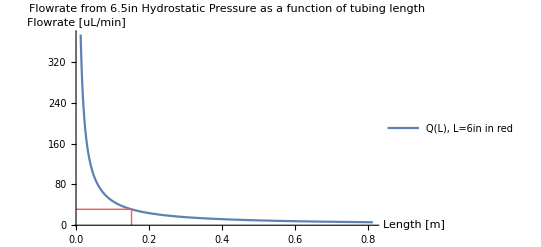

```mathematica
L0=0.152;expr1=Pmax6/RH[L]*(60*10^6); (* For 2D Laminar Flow, ΔP=Q*R *)
expr2= Line[{{{L0,0},{L0,expr1/. L->L0}},{{0,expr1/. L->L0},{L0,expr1/. L->L0}}}];
(*For tubing lengths between 0.5in=0.0127m and 32in=0.813m*)


Plot[Legended[expr1,"Q(L), L=6in in red"],{L,0.0127,0.813},AxesLabel->{"Length [m]","Flowrate [uL/min]"},PlotRange->All,PlotLabel->"Flowrate from 6.5in Hydrostatic Pressure as a function of tubing length",Epilog->{Lighter@Red, expr2}]
```

```mathematica
For[i=1,i<=6,i++,Print["P=",Pmax6,"Pa, L =",i*6," inches, Qmax =",Pmax6/RH[i*L0]*(60*10^6),"[uL/min]"]]
```

P=1610Pa, L =6 inches, Qmax =31.2796[uL/min]

P=1610Pa, L =12 inches, Qmax =15.6398[uL/min]

P=1610Pa, L =18 inches, Qmax =10.4265[uL/min]

P=1610Pa, L =24 inches, Qmax =7.8199[uL/min]

P=1610Pa, L =30 inches, Qmax =6.25592[uL/min]

P=1610Pa, L =36 inches, Qmax =5.21327[uL/min]

```mathematica
For[i=1,i<=6,i++,Print["P=",Pmax14,"Pa, L =",i*6," inches, Qmax =",Pmax14/RH[i*L0]*(60*10^6),"[uL/min]"]]
```

P=3602Pa, L =6 inches, Qmax =69.9808[uL/min]

P=3602Pa, L =12 inches, Qmax =34.9904[uL/min]

P=3602Pa, L =18 inches, Qmax =23.3269[uL/min]

P=3602Pa, L =24 inches, Qmax =17.4952[uL/min]

P=3602Pa, L =30 inches, Qmax =13.9962[uL/min]

P=3602Pa, L =36 inches, Qmax =11.6635[uL/min]